# OSNOVNE OBLIKE

## NAJPOGOSTEJŠE, IZ NJIH LAHKO SESTAVIMO, ∀ KAR HOČEMO



{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[{#}]&/@{
	Circle[{0,0},3],
	Disk[{0,0},3],
	Point[{0,0}]
}
```

Pri Point, Sphere, Line, Polygon in podobnih stvareh jih lah direktno več naštejemo

Pri Graphics[{}] in Graphics3D[{}] lah naštejemo pred obliko razne lastnosti (barva,...). To še pride.

```mathematica
{


Graphics3D@Sphere[{0,0,0},3],

Graphics3D[{
	Blue,
	Sphere[{0,0,0},3]
}],

Graphics3D[{
	Green,
	Sphere[{{0,0,0},{1,1,1},{3,3,3}},{1,2,3}]
}]


}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

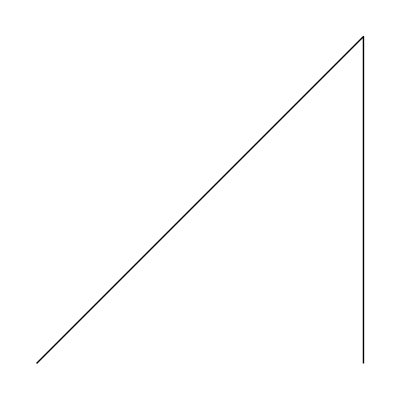
{-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
{
Graphics@Line[{{0,0}, {1,1}, {1,0}}],

Graphics3D[{
	Red,
	Line[{
		{{0,0,0}, {1,1,0}, {1,0,0}, {0,1,1}},
		{{1,1,.7}, {1,.7,1}, {.7,1,1},{1,1,.7}}
	}]
}],

Graphics3D[{
	Red,
	Tube[{
		{{0,0,0}, {1,1,0}, {1,0,0}, {0,1,1}},
		{{1,1,.7}, {1,.7,1}, {.7,1,1},{1,1,.7}}
	}]
}]
}
```

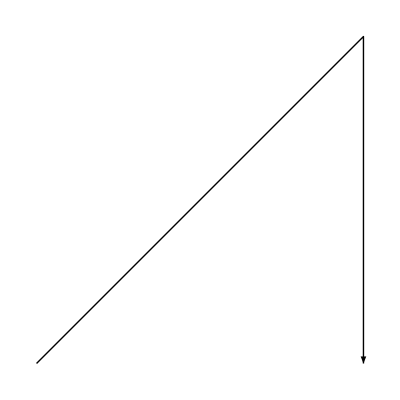
{-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
{
Graphics@Arrow[{{0,0}, {1,1}, {1,0}}],

Graphics3D[{
	Red,
	Arrow[{
		{{0,0,0}, {1,1,0}, {1,0,0}, {0,1,1}},
		{{1,1,.7}, {1,.7,1}, {.7,1,1},{1,1,.7}}
	}]
}],

Graphics3D[{
	Red,
	Arrowheads@.1,
	Arrow@Tube[{
			{{0,0,0}, {1,1,0}, {1,0,0}, {0,1,1}},
			{{1,1,.7}, {1,.7,1}, {.7,1,1},{1,1,.7}}
		},
		.01
	]
}]
}
```

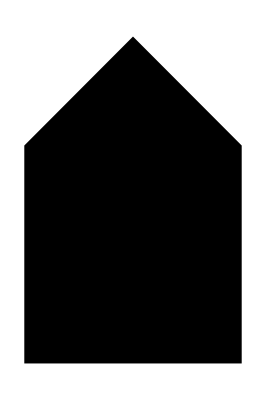
{-Graphics-,-Graphics3D-}

```mathematica
{
Graphics@Polygon[{{0,0},{1,0},{1,1},{.5,1.5},{0,1}}],

Graphics3D@Polygon[
{
	{{1,0,0},{0,1,0},{0,0,1}},
	{{-1,0,0},{0,1,0},{0,0,1}},
	{{1,0,0},{0,-1,0},{0,0,1}},
	{{-1,0,0},{0,-1,0},{0,0,1}},
	{{1,0,0},{0,1,0},{0,0,-1}},
	{{-1,0,0},{0,1,0},{0,0,-1}},
	{{1,0,0},{0,-1,0},{0,0,-1}},
	{{-1,0,0},{0,-1,0},{0,0,-1}},
	{{-1,-1,-1},{1,-1,-1},{2,2,-1},{-1,1,-1}}
}]
}
```

```mathematica
ogl = {{0, 0, 0}, {2, 0, 0}, {2, 2, 0}, {0, 2, 0}, {1, 1, 1}, {2,0,2}, {2,2,2}};
indjijiP = {{1, 2, 5}, {2, 3, 5}, {3, 4, 5}, {4, 1, 5}};
indjijiL = {7,5,6};

Graphics3D[{
	GraphicsComplex[ogl, {Polygon@indjijiP, Line@indjijiL}]   (*Line da ogrodje*)
}]
```

-Graphics3D-

## TUDI VČASIH PRAV PRIDEJO

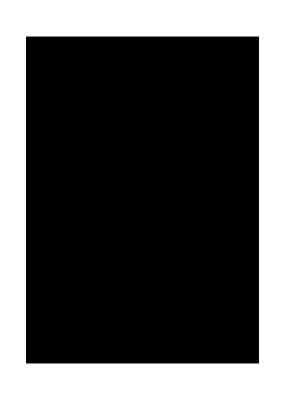
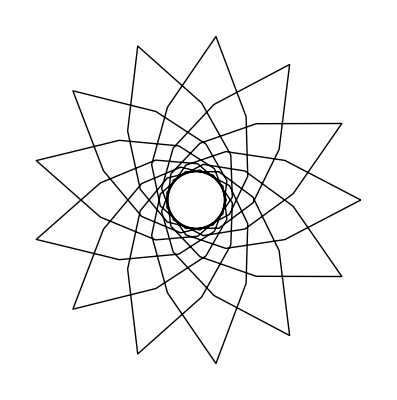
{-Graphics-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics-}

```mathematica
{
Graphics@Rectangle[{1,-2},{-4,5}],
Graphics3D@Cuboid[{1,-2,3},{-4,5,6}],
Graphics3D@Cylinder[{{1,2,3},{4,5,6}},.5],
Graphics3D@Cone[{{1,2,3},{4,5,6}},.5],
Graphics@BezierCurve@Table[{Cos[2 k Pi/13],Sin[2 k Pi/13]},{k,0,156,4}]
}
```

# NAPISI

```mathematica
Quit[]
```

```mathematica
Graphics3D@Style[
	Text["√(a/b)",{1,2,3}],
	RGBColor[{0,.5,1}],30,Bold,FontFamily->"Comic Sans MS"
]
```

-Graphics3D-

```mathematica
HoldForm[√(1+3/4)+a+a]
```

√(1+3/4)+a+a

Tako pa narišem latex enačbe

Učasih za te FontSize ne deluje. V tem primeru uporabimo Magnification->

Je pa vseskup rahlo butasto, sploh za barvo ibrat...

LATEX je itak butast

```mathematica
(*
Remove["Global`*"];
*)

ResourceFunction["MaTeXInstall"][];
Needs["MaTeX`"];
ConfigureMaTeX["pdfLaTeX" -> "c:\\Program Files\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe"];
ConfigureMaTeX["Ghostscript" -> "C:\\Program Files\\gs\\gs9.56.1\\bin\\gswin64c.exe"];
ResourceFunction["MaTeXInstall"];

SetOptions[MaTeX,"Preamble"->{
"\\usepackage{color,bm}",
"\\definecolor{črna}{rgb}{0,0,0}",
"\\definecolor{modra}{rgb}{0,0,1}",
"\\definecolor{zelena}{rgb}{0,1,0}",
"\\definecolor{rdeča}{rgb}{1,0,0}",
"\\definecolor{cian}{rgb}{0,1,1}",
"\\definecolor{magenta}{rgb}{1,0,1}",
"\\definecolor{rumena}{rgb}{1,1,0}",
"\\definecolor{oranžna}{rgb}{1,0.5688888888888889,0}",
"\\definecolor{bela}{rgb}{1,1,1}",
"\\definecolor{siva}{rgb}{.3,.3,.3}"
}];
```

```mathematica
Graphics@Text[
	MaTeX["\\color{oranžna}{w\\bm{\\hat{\\imath}}=\\bm{\\left(1,0\\right)}}",FontSize->50],
	{2,1.3}
]
```

-Graphics-

```mathematica
MaTeX[√(a/b+c)]
```

-Graphics-

```mathematica
TeXForm[√(a/b+c)]
```

\sqrt{\frac{a}{b}+c}

```mathematica
TeXForm@HoldForm[(1+√(a/b+c)+1+1)({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})]
```

\left(1+\sqrt{\frac{a}{b}+c}+1+1\right) \left(
\begin{array}{ccc}
 1 & 2 & 3 \\
 4 & 5 & 6 \\
 7 & 8 & 9 \\
\end{array}
\right)

```mathematica
MaTeX@%
```

-Graphics-

# Show

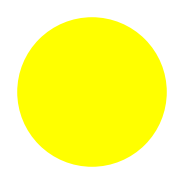

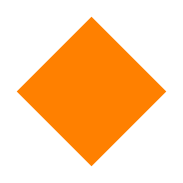

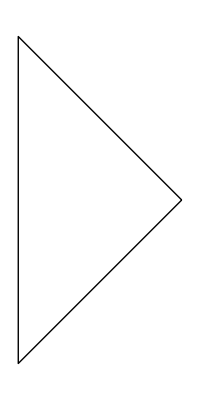
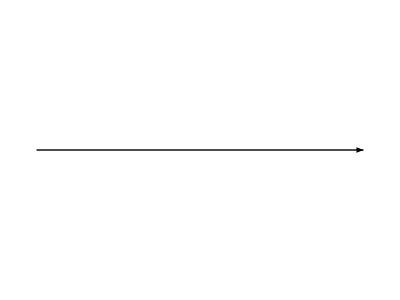
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
grafika1=Graphics[{Yellow,Disk[{0,0}]}]
grafika2=Graphics[{Orange,Polygon@{{0,0},{1,-1},{2,0},{1,1}} }]
SeznamGrafik={
	Graphics@Line@{{0,0},{-1,1},{-1,-1},{0,0}},
	Graphics@Text["NekiNeki",{0,.5}],
	Graphics@Arrow@{{1,0},{2,0}}
}
```

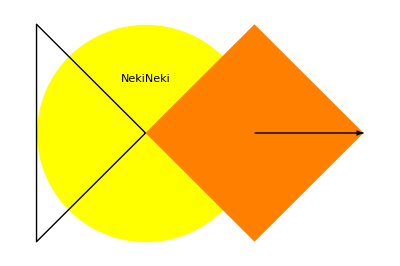

```mathematica
Show[
	grafika1,
	grafika2,
	SeznamGrafik
]
```

Lah maš tut sezname seznamov grafik,... Vse je ok, dela zanesljivo

# LASTNOSTI

Tuki je zlo lepo zbrano praktično vse in skor nč več, kar se splača poznat

https://reference.wolfram.com/language/guide/GraphicsDirectives.html

Rahlo je čudno, ampak najprej je treba naštet lastnosti in šele potem kaj rišemo

Nekaj primerčkov

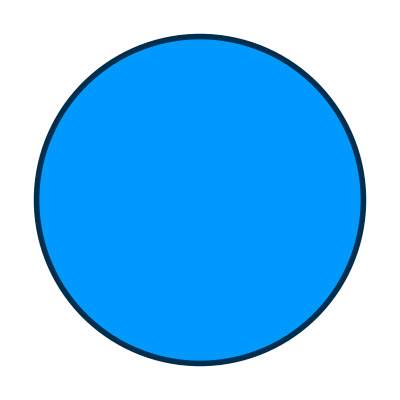

```mathematica
Graphics[{
	EdgeForm@{RGBColor[.3{0,.6,1}],  Thickness@.01,  Dashing@{.1,.05}},
	FaceForm@{RGBColor@{0,.6,1}},
	Disk[]
}]
```

```mathematica
kvadrat=Polygon@{{0,0},{1,0},{1,1},{0,1}};

Show[
Graphics[{
	EdgeForm@{RGBColor[.3{0,.6,1}],  Thickness@.04, JoinForm@"Miter"},
	FaceForm@{RGBColor@{.6,.6,1}},
	kvadrat
}],

Graphics[{
	RGBColor[.3{0,.6,1}],
	HatchFilling[20°,.1,10],
	kvadrat
}]
]
```

-Graphics-

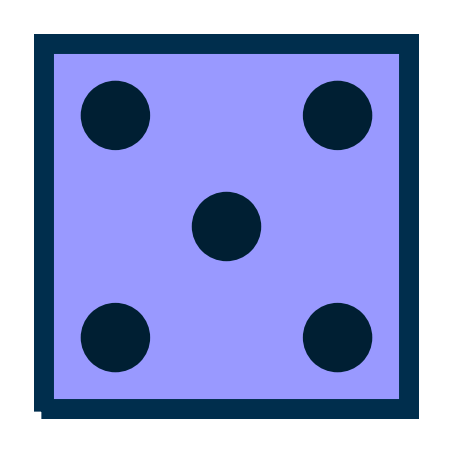

```mathematica
kvadrat=Polygon@{{0,0},{1,0},{1,1},{0,1}};

odmik=.2;
Show[
Graphics[{
	EdgeForm@{RGBColor[.3{0,.6,1}],  Thickness@.04, JoinForm@"Round"},
	FaceForm@{RGBColor@{.6,.6,1}},
	kvadrat
}],
Graphics[{
	RGBColor[.2{0,.6,1}], PointSize@.2,
	Point@{{odmik,odmik},{1-odmik,odmik},{1-odmik,1-odmik},{odmik,1-odmik},{.5,.5}}
}]
]
```

PointSize:    delež širine plota

AbsolutePointSize    premer, ampak to ni dobr, ker se spreminja razmerje, ko povečuješ/zmanjšuješ skico. 
Isto za AbsoluteThickness in podobno.

Barvo  izberemo tudi s klikom na Chose Color

-Graphics-

-Graphics-

-Graphics-

glej tudi:

ColorConvert[color,colspace]

https://www.youtube.com/watch?v=gnUYoQ1pwes&t=1767s&ab_channel=KuvinaSaydaki

```mathematica
Graphics[{ 
	LinearGradientFilling[{0,.3,1}->{RGBColor[.67, .86, 1.], RGBColor[.012, .59,1.],Purple},   30°],
	Polygon[{{0,0},{1,0},{1,1}}]
}]
```

-Graphics-

Kako se to dela pri 3D grafikah in bolj na splošno bo pri naslovu TEKSTURE

Tudi Show ma razne opcije

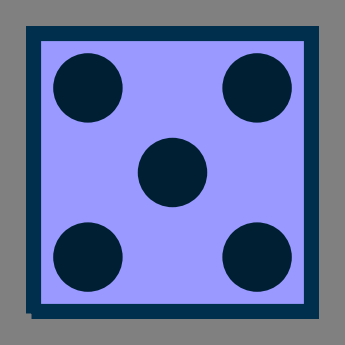
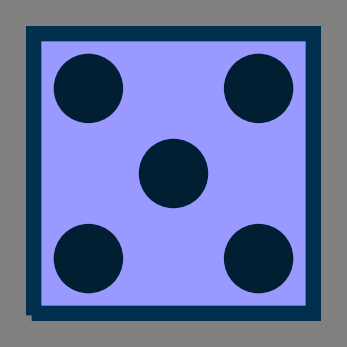
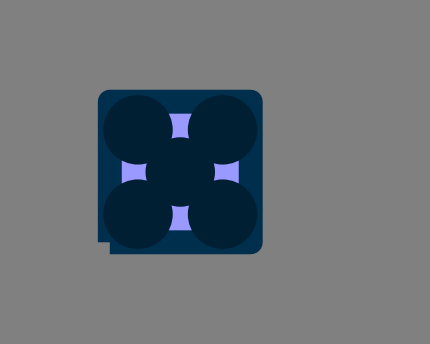

```mathematica
Show[
	-Graphics-,
	PlotRange->#,
	Background->Gray
]&/@{Automatic,All,{{-.5,2},{-.5,1.5}}}
```

Tudi vidimo, zakaj je bolje uporabljati Disk, kot pa Point in podobno

probite isto narisat z Disk

Point uporabimo, ko mamo za narisat kak miljon toč in bi z Disk štekalo

# TABELA GRAFIK

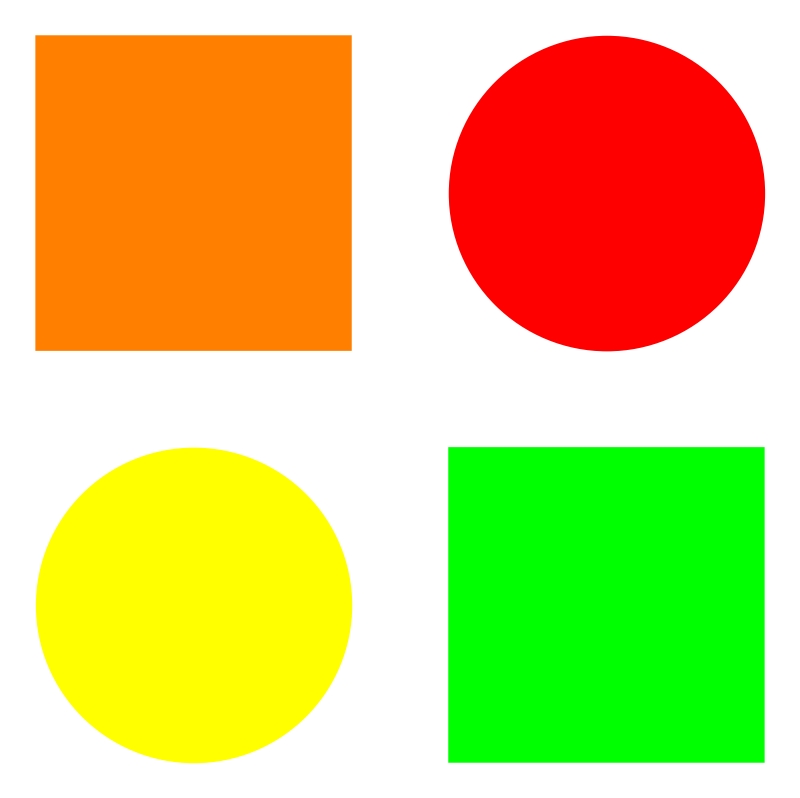

```mathematica
GraphicsGrid[({{Graphics[{Orange,Rectangle[]}], Graphics[{Red,Disk[]}]}, {Graphics[{Yellow,Disk[]}], Graphics[{Green,Rectangle[]}]}}),Frame->All]
```

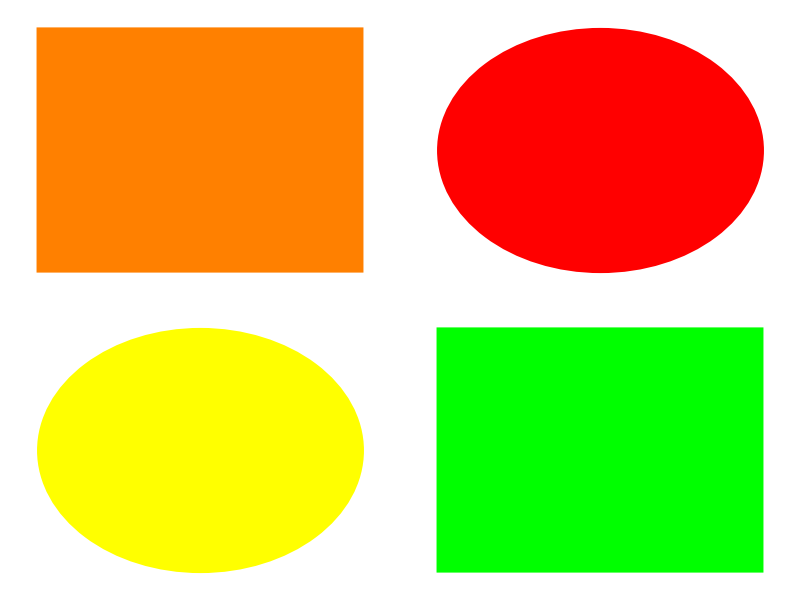

```mathematica
Grid[({{Graphics[{Orange,Rectangle[]}], Graphics[{Red,Disk[]}]}, {Graphics[{Yellow,Disk[]}], Graphics[{Green,Rectangle[]}]}}),Frame->All]
```

Ampak pri določenih grafih lah kaj zgine. V tem primeru pretvorimo vse v slike in uporabmo ImageAssemble

# KOTI

```mathematica
(*
-TčjiKota je: {krak1, vrh, krak2}
-obr je obroba
-FaktZamikaKot: premakne napis v smeri navzven kota za ta faktor*VelNap
*)
PlotajKot2D[TčjiKota_,Rkota_,Bnot_,Bobr_,DebObr_,NapTex_,VelNap_,FaktZamikaKot_]:=(
SetOptions[MaTeX,"Preamble"->{
"\\usepackage{color,bm}",
"\\definecolor{Bobr}{rgb}"<>ToString[Bobr[[;; 3]]]
}];
VektKota1=TčjiKota[[1]]-TčjiKota[[2]];
VektKota2=TčjiKota[[3]]-TčjiKota[[2]];
φminφmax=(ToPolarCoordinates /@ {VektKota1, VektKota2})[[;;,2]];
	
Show[
	Graphics[{RGBColor@Bnot, Disk[TčjiKota[[2]], Rkota, φminφmax]}],
	Graphics[{RGBColor@Bobr, Circle[TčjiKota[[2]], Rkota, φminφmax]}],
	Graphics[Text[
		MaTeX["\\color{Bobr}"<>NapTex,
		FontSize->VelNap],
		TčjiKota[[2]]+(Rkota-FaktZamikaKot VelNap) Normalize[Normalize@VektKota1+Normalize@VektKota2]
	]]
]
);
```

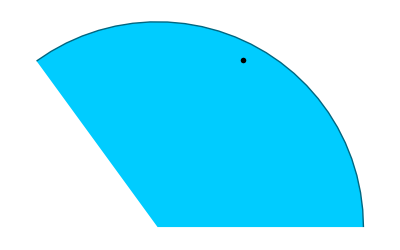

```mathematica
PlotajKot2D[
	{{1,0},{0,0},FromPolarCoordinates@{1.3,.7π}}+Threaded[{1,2},2],
	1.4,{0,.8,1},.5{0,.8,1},.001,"\\varphi",20,.006
]
```

```mathematica
(*
-TčjiKota je: {krak1, vrh, krak2}
-obr je obroba
-FaktZamikaKot: premakne napis v smeri navzven kota za ta faktor*VelNap
*)
PlotajKot3D[TčjiKota_,Rkota_,Bnot_,Bobr_,DebObr_,Npodkotov_,NapTex_,VelNap_,FaktZamikaKot_]:=(
SetOptions[MaTeX,"Preamble"->{
"\\usepackage{color,bm}",
"\\definecolor{Bobr}{rgb}"<>ToString[Bobr[[;; 3]]]
}];
VektKota1=TčjiKota[[1]]-TčjiKota[[2]];
VektKota2=TčjiKota[[3]]-TčjiKota[[2]];
kot=VectorAngle[VektKota1,VektKota2];
RMjikota=Table[RotationMatrix[θkota,{VektKota1,VektKota2}],{θkota,0,kot,kot/Npodkotov}];
LokKota=(TčjiKota[[2]]+Rkota # . Normalize[VektKota1])&/@RMjikota;

DaljiceLoka=Partition[LokKota,2,1];
TrikotnikiKota={
	DaljiceLoka[[;;,1]],
	Table[TčjiKota[[2]],Npodkotov],
	DaljiceLoka[[;;,2]]
}ᵀ;
	
Show[
	Graphics3D[{RGBColor[Bnot],EdgeForm[],Polygon@#}]&/@TrikotnikiKota,
	Graphics3D[{RGBColor[Bobr],Thickness->DebObr,Line@LokKota}],
	Graphics3D[Text[
		MaTeX["\\color{Bobr}"<>NapTex,
		FontSize->VelNap],
		TčjiKota[[2]]+(Rkota-FaktZamikaKot VelNap) Normalize[Normalize@VektKota1+Normalize@VektKota2]
	]]
]
);
```

```mathematica
PlotajKot3D[
	{{1,0,0},{0,0,0},{3,2,1}},   1.4,
	{0,.8,1,.5},.5{0,.8,1},
	.003, 100, ToString@TeXForm[(α+β)/3] ,15,.008
]
```

-Graphics3D-

# OSNOVNO PLOTANJE

https://reference.wolfram.com/language/guide/DataVisualization.html

https://reference.wolfram.com/language/guide/GraphicsOptionsAndStyling.html

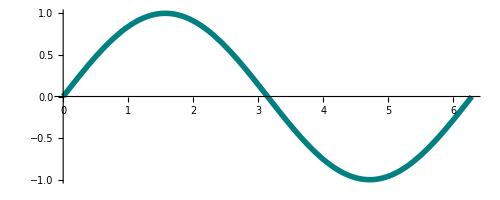

```mathematica
Plot[
	Sin[x],{x,0,2π},
	PlotStyle -> {RGBColor[.5{0,1,1}],Thickness@.01},
	AspectRatio->Automatic
]
```

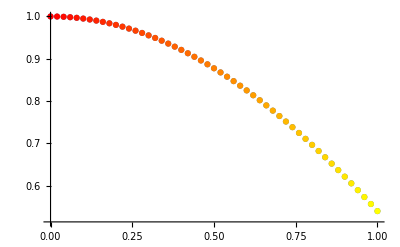

```mathematica
ListPlot[
	Table[Style[
		{x,Cos@x},           (*f[x]*)
		RGBColor@{1,x,0}     (*barva[x]*)
	],{x,0,1,.02}]
]
```

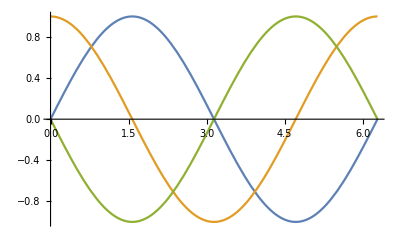

```mathematica
Plot[{Sin@x,Cos@x,Sin[x-π]},{x,0,2 π}]
```

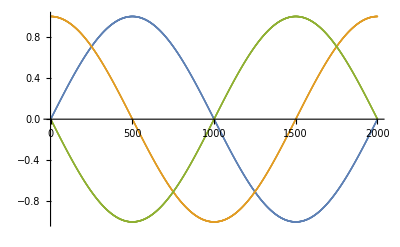

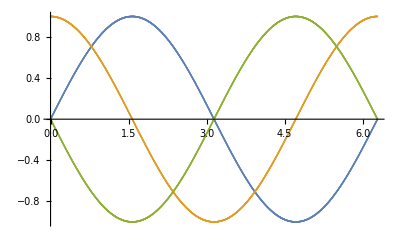

```mathematica
ran=N@Subdivide[0,2π,2000];
slikeke={slike1,slike2,slike3}={Sin@ran,Cos@ran,Sin[ran-π]};
točkečke={točke1,točke2,točke3}=Transpose[{Table[ran,3],slikeke},InversePermutation@{2,3,1}];

ListPlot@slikeke
ListPlot@točkečke
```

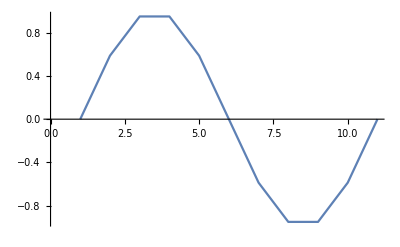
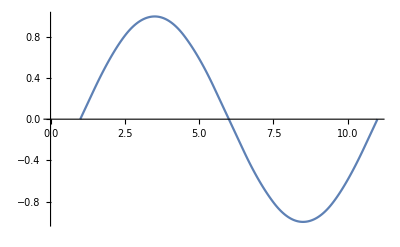

```mathematica
ran=N@Subdivide[0,2π,10];
slike=Sin@ran;

{
ListLinePlot@slike,
ListLinePlot[slike,InterpolationOrder->2]
}
```

```mathematica
točke=Flatten[Table[{r Cos@φ,r Sin@φ, r^2},{r,0,1,.1},{φ,0,360°-10°,10°}],1];

{
ListPlot3D@točke,
ListLinePlot3D@točke,
ListPointPlot3D@točke
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{
Plot3D[
	Sin[x]Sin[y], {x,-5,5},{y,-5,5 },
	Mesh -> None,
	PlotPoints->150, (*MaxRecursion->,*)
	PlotStyle -> {RGBColor[{0,.7,1}]}
 ],
 
Plot3D[
	Sin[x]Sin[y], {x,-5,5},{y,-5,5 },
	Mesh -> {5,3}, 
	MeshStyle->{RGBColor[.2{0,.7,1}], Thickness@.003},
	PlotPoints->150, (*MaxRecursion->,*)
	PlotStyle -> {RGBColor[{0,.7,1}]},
	BoxRatios->Automatic
]
}
```

{-Graphics3D-,-Graphics3D-}

Večina sledečih grafov ma popolnoma enake možne opcije, kot tedva

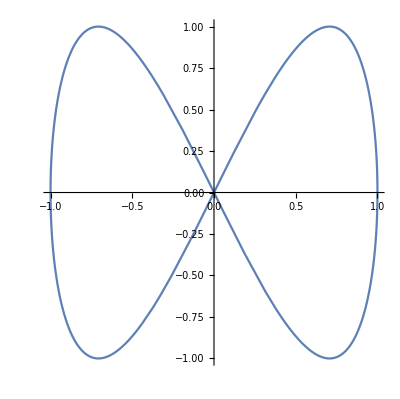
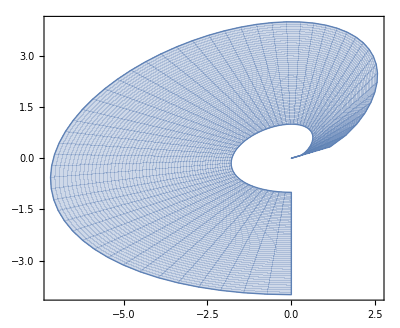
{-Graphics-,-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
{
ParametricPlot[{Sin[u], Sin[2 u]}, {u, 0, 2 Pi}],
ParametricPlot[r^2 { Sqrt[t] Cos[t], Sin[t]}, {t, 0, 3 Pi/2}, {r, 1, 2}],
ParametricPlot3D[{Cos[u], Sin[u] + Cos[v], Sin[v]}, {u, 0,  2 π}, {v, -π, π}],
ParametricPlot3D[{Sin[u], Cos[u], u/10}, {u, 0, 20}]
}
```

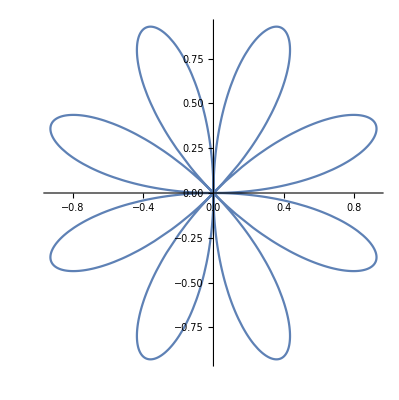
{-Graphics-,-Graphics3D-}

```mathematica
{
PolarPlot[Sin[4 θ],{θ,0,2 Pi}],
SphericalPlot3D[1 + 2 Cos[2 θ], {θ, 0, Pi}, {ϕ, 0, 2 Pi}]
}
```

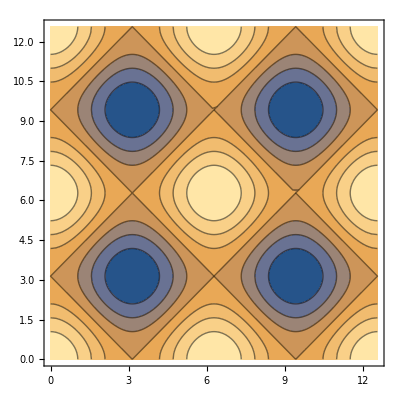
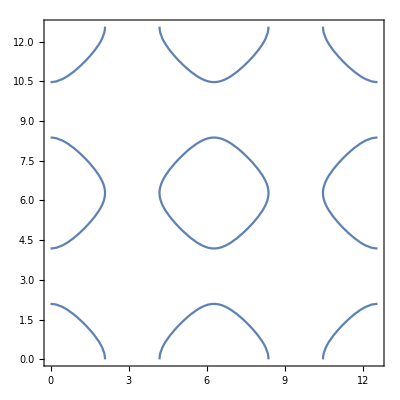
{-Graphics-,-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
{
ContourPlot[Cos[x] + Cos[y], {x, 0, 4 Pi}, {y, 0, 4 Pi}],
ContourPlot[Cos[x] + Cos[y] == 1/2, {x, 0, 4 Pi}, {y, 0, 4 Pi}],
ContourPlot3D[x^3 + y^2 - z^2, {x, -2, 2}, {y, -2, 2}, {z, -2, 2}],
ContourPlot3D[x^3 + y^2 - z^2 == 0, {x, -2, 2}, {y, -2, 2}, {z, -2, 2}]
}
```

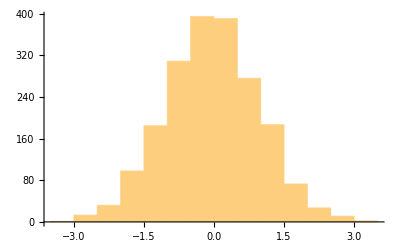

```mathematica
Histogram[RandomVariate[NormalDistribution[0,1],2000],15]
```

Pozor tukej je BoundaryStyle namesto EdgeForm

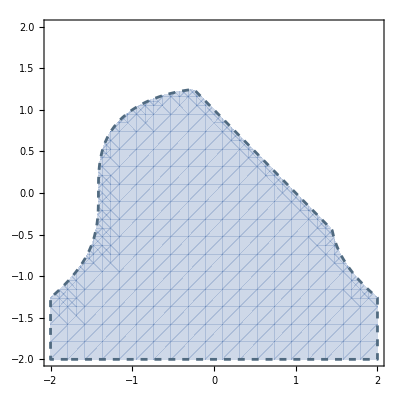
{-Graphics-,-Graphics3D-}

```mathematica
{
RegionPlot[
	{x^2+y^3<2&&x+y<1}, (*območja*)
	{x,-2,2},{y,-2,2},   (*range*)
	BoundaryStyle->{Dashed,Thickness@.005,RGBColor[.5{0.63,0.83,1.}]}
],

RegionPlot3D[
	x y z < 1, {x, -5, 5}, {y, -5, 5}, {z, -5, 5}, 
	Mesh -> 10, PlotPoints->100,
	PlotStyle -> {RGBColor@{0,1,1,.8}},BoundaryStyle->{Blue, Thick}	
]
}
```

# OZNAČEVANJE GRAFOV

https://reference.wolfram.com/language/guide/GraphicsAnnotationAndAppearance.html

## OPCIJE GRAFA

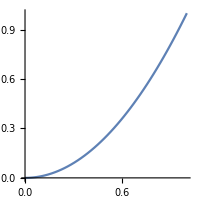

```mathematica
Plot[x^2,{x,0,1},AspectRatio->Automatic]
```

```mathematica
AbsoluteOptions@%
```

{AlignmentPoint→Center,AspectRatio→1.06667,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0.,0.},AxesStyle→{{},{}},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction→Identity,Epilog→{},FormatType→TraditionalForm,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameStyle→{{{},{}},{{},{}}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle→{{{},{}},{{},{}}},GridLines→None,GridLinesStyle→{{LineColor→GrayLevel[0.5],LineOpacity→0.4,FrontFaceColor→GrayLevel[0.5],BackFaceColor→GrayLevel[0.5],FrontFaceOpacity→0.4,BackFaceOpacity→0.4,GraphicsColor→GrayLevel[0.5],Opacity→0.4,FontColor→GrayLevel[0.5],FontOpacity→0.4},{LineColor→GrayLevel[0.5],LineOpacity→0.4,FrontFaceColor→GrayLevel[0.5],BackFaceColor→GrayLevel[0.5],FrontFaceOpacity→0.4,BackFaceOpacity→0.4,GraphicsColor→GrayLevel[0.5],Opacity→0.4,FontColor→GrayLevel[0.5],FontOpacity→0.4}},ImageMargins→0.,ImagePadding→{{9.90956,0.5},{0.5,0.5}},ImageSize→{360.,373.896},ImageSizeRaw→Automatic,LabelStyle→{},Method→{DefaultBoundaryStyle→Automatic,DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},DefaultMeshStyle→AbsolutePointSize[6],ScalingFunctions→None,CoordinatesToolOptions→{DisplayFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),CopiedValueFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotLabel→None,PlotRange→{{-3.46945×10^-18,1.},{0.,1.}},PlotRangeClipping→True,PlotRangePadding→{{0.0208333,0.0208333},{0.0555556,0.0555556}},PlotRegion→{{0.,1.},{0.,1.}},PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→{{{0.,0.0,{0.0152559,0.}},{0.05,,{0.00915357,0.}},{0.1,,{0.00915357,0.}},{0.15,,{0.00915357,0.}},{0.2,0.2,{0.0152559,0.}},{0.25,,{0.00915357,0.}},{0.3,,{0.00915357,0.}},{0.35,,{0.00915357,0.}},{0.4,0.4,{0.0152559,0.}},{0.45,,{0.00915357,0.}},{0.5,,{0.00915357,0.}},{0.55,,{0.00915357,0.}},{0.6,0.6,{0.0152559,0.}},{0.65,,{0.00915357,0.}},{0.7,,{0.00915357,0.}},{0.75,,{0.00915357,0.}},{0.8,0.8,{0.0152559,0.}},{0.85,,{0.00915357,0.}},{0.9,,{0.00915357,0.}},{0.95,,{0.00915357,0.}},{1.,1.0,{0.0152559,0.}}},{{-0.05,,{0.00915357,0.}},{0.,0.0,{0.0152559,0.}},{0.05,,{0.00915357,0.}},{0.1,,{0.00915357,0.}},{0.15,,{0.00915357,0.}},{0.2,0.2,{0.0152559,0.}},{0.25,,{0.00915357,0.}},{0.3,,{0.00915357,0.}},{0.35,,{0.00915357,0.}},{0.4,0.4,{0.0152559,0.}},{0.45,,{0.00915357,0.}},{0.5,,{0.00915357,0.}},{0.55,,{0.00915357,0.}},{0.6,0.6,{0.0152559,0.}},{0.65,,{0.00915357,0.}},{0.7,,{0.00915357,0.}},{0.75,,{0.00915357,0.}},{0.8,0.8,{0.0152559,0.}},{0.85,,{0.00915357,0.}},{0.9,,{0.00915357,0.}},{0.95,,{0.00915357,0.}},{1.,1.0,{0.0152559,0.}},{1.05,,{0.00915357,0.}}}},TicksStyle→{{},{}}}

## OBIČAJEN FIZIKALNI GRAF

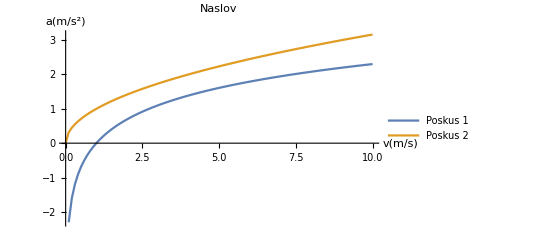

```mathematica
ListLinePlot[
	Table[{{x,Log@x},{x,√x}}, {x, 0, 10, 0.1}]ᵀ, 
	
	PlotRange -> All,
	LabelStyle->{FontSize->15},
	AxesLabel->{v[m/s],a[m/s^2]},          (*((StringForm@#)&/@{"v[m/s]","a[m/s^2]"})*)
	PlotLegends -> Placed[{"Poskus 1","Poskus 2"},Right],
	PlotLabel->Style["Naslov"]
 
]
```

## KAJ SE ŠE DA SPREMENIT

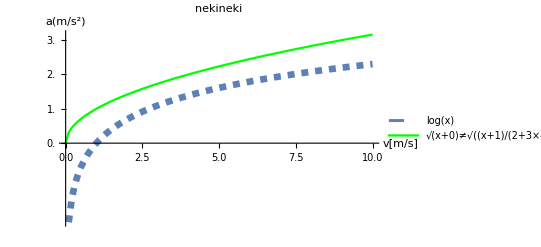

```mathematica
ListLinePlot[
(*  {točke grafa 1,  točke grafa 2}   *)
	Table[{{x,Log@x},{x,√x}}, {x, 0, 10, 0.1}]ᵀ, 
(*  sicer {{xmin,xmax},{ymin,ymax}}  *)
	PlotRange -> All,
(*  slog grafa 1, slog grafa 2*)
	PlotStyle->{{Dashed,Thickness@.012},{Green}},
(*  osnovni slog napisov*)
	LabelStyle->{Bold,Brown, FontSize->10},
(*  slog osi 1, slog osi 2*)	
	AxesStyle->{{Gray,Thickness@.01},{RGBColor[.8{0,1,1}]}  },
(*  enote in količine*)
	AxesLabel->{StringForm["v[m/s]"],HoldForm[a[m/s^2]]},
(*  slog osi 1, slog osi 2*)
	PlotLegends -> Placed[{Style["log(x)",Orange], HoldForm[√(x+0)!=√((x+1)/(2+3×4))]},Right],
(*  črtice*)
	Ticks->{Automatic,Range[0,3,.5]},
(*  slog črtic*)
	TicksStyle->{Thin,Automatic},
(*  naslov grafa 2*)
	PlotLabel->Style["nekineki",Blue,Italic,FontFamily->"Comic Sans MS",FontSize->15]
 
]
(*NAMESTO Axes... mamo lah tut Axes..., vse opcije in to na enak način*)
```

## 3D PLOTI

Podobno

# NAPREDNO PLOTANJE

## RegionFunction

```mathematica
Grid[
{
{
SphericalPlot3D[
 1 + Sin[5 θ] Sin[5 ϕ]/5, {θ, 0, Pi}, {ϕ, 0, 
  2 Pi}, Mesh -> None, RegionFunction -> (#1 > 0.9 &), 
 PlotStyle -> FaceForm[Orange, Yellow]],
 
 SphericalPlot3D[
 1 + Sin[5 θ] Sin[5 ϕ]/5, {θ, 0, Pi}, {ϕ, 0, 
  2 Pi}, Mesh -> None, RegionFunction -> (#2 > 0.9 &), 
 PlotStyle -> FaceForm[Orange, Yellow]],
 
SphericalPlot3D[
 1 + Sin[5 θ] Sin[5 ϕ]/5, {θ, 0, Pi}, {ϕ, 0, 
  2 Pi}, Mesh -> None, RegionFunction -> (#3 > 0.9 &), 
 PlotStyle -> FaceForm[Orange, Yellow]]
 },
 
{ 
 SphericalPlot3D[
 1 + Sin[5 θ] Sin[5 ϕ]/5, {θ, 0, Pi}, {ϕ, 0, 
  2 Pi}, Mesh -> None, RegionFunction -> (#4 > 0.9 &), 
 PlotStyle -> FaceForm[Orange, Yellow]],
 
 SphericalPlot3D[
 1 + Sin[5 θ] Sin[5 ϕ]/5, {θ, 0, Pi}, {ϕ, 0, 
  2 Pi}, Mesh -> None, RegionFunction -> (#5 > 0.9 &), 
 PlotStyle -> FaceForm[Orange, Yellow]],
 
SphericalPlot3D[
 1 + Sin[5 θ] Sin[5 ϕ]/5, {θ, 0, Pi}, {ϕ, 0, 
  2 Pi}, Mesh -> None, RegionFunction -> (#6 > 0.9 &), 
 PlotStyle -> FaceForm[Orange, Yellow]]
 }
 },
 
 
 Frame->All]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
φ=107°;
Plot3D[x^2-y^2,{x,-3,3},{y,-3,3},RegionFunction->((2<#1^2+#2^2<9&&ToPolarCoordinates[{#1,#2}][[2]]<φ)&)]
```

-Graphics3D-

## Texture

ColorFunction: glede na relativne koordinate med 0 in 1(*po stranicah plot ranga*)

```mathematica
Plot3D[Sin[x y]+1, {x, 0, 3}, {y, 0, 3}, 
 ColorFunction -> (RGBColor[(1-#3){0,1,1}]&),
 Mesh->None,PlotPoints->100]
```

-Graphics3D-

Za večkotnike podamo relativne koordinate njihovih oglišč,  na sliki. Koordinate so med 0 in 1.

```mathematica
slika=-Graphics-;

Graphics[{
	Texture@slika, 
    Polygon[{{0, 0}, {1, 0}, {1/2, 1}}, 
    VertexTextureCoordinates -> #]
}]&/@{
{{0, 0}, {1, 0}, {0, 1}},
{{0, 0}, {1, 0}, {1/2, 1}},
{{0, 0}, {1, 0}, {1, 1}},
RandomReal[{0,1},{3,2}]
}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},PlotStyle->Texture@slika,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{1.16^v Cos[v] (1 + Cos[u]),
-1.16^v Sin[v] (1 + Cos[u]),
-2 1.16^v (1 + Sin[u])},
{u, 0, 2 Pi}, {v, -15, 6}, 
PlotStyle -> {Specularity[White, 30], Texture@slika},
TextureCoordinateFunction -> ({#4, 2 #5} &), 
PlotPoints->200,
Lighting -> "Neutral", Mesh -> None, PlotRange -> All]
```

-Graphics3D-

```mathematica
vtc = {{0, 0}, {1, 0}, {1, 1}, {0, 1}};
coords = {{{0, 0, 0}, {0, 1, 0}, {1, 1, 0}, {1, 0, 0}}, {{0, 0, 
     0}, {1, 0, 0}, {1, 0, 1}, {0, 0, 1}}, {{1, 0, 0}, {1, 1, 0}, {1, 
     1, 1}, {1, 0, 1}}, {{1, 1, 0}, {0, 1, 0}, {0, 1, 1}, {1, 1, 
     1}}, {{0, 1, 0}, {0, 0, 0}, {0, 0, 1}, {0, 1, 1}}};

Graphics3D[{FaceForm@Texture@-Graphics-, 
  Polygon[coords, VertexTextureCoordinates -> Table[vtc, {6}]]
 }, 
Lighting -> "Neutral"]
```

-Graphics3D-

```mathematica
Graphics3D[{FaceForm[Texture[-Graphics-], Texture[-Graphics-]], 
  Polygon[coords, VertexTextureCoordinates -> Table[vtc, {6}]]}, 
 Lighting -> "Neutral"]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1 , {u, 0, Pi}, {v, 0, 2 Pi}, Mesh -> None,
PlotPoints->200,
 TextureCoordinateFunction -> ({#5, 1 - #4} &), 
 PlotStyle -> {Specularity[White, 10], Texture[#]}, Lighting -> "Neutral", 
 Axes -> False, RotationAction -> "Clip"]&/@{-Graphics-,-Graphics-}
```

{-Graphics3D-,-Graphics3D-}

https://reference.wolfram.com/language/ref/Texture.html

```mathematica
Graphics3D[{HatchShading[.6, Blue], 
  KnotData["SolomonSeal", "ImageData"]}, Lighting -> "Accent", Boxed->False]
```

-Graphics3D-

https://reference.wolfram.com/language/ref/MaterialShading.html

## RAZSVETLJAVA

https://reference.wolfram.com/language/ref/Lighting.html

```mathematica
Graphics3D[{Gray, Sphere[]}, Lighting -> #]&/@{Automatic,"Neutral"}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
col = {Red, Green, Blue};
objs = Graphics3D[{Specularity[White, 2], EdgeForm[], 
    Cylinder[{{2, 2, 0}, {2, 2, 4}}], 
    Cylinder[{{6, 2, 0}, {6, 2, 4}}], 
    Cylinder[{{10, 2, 0}, {10, 2, 4}}]}];
walls = ParametricPlot3D[{{u, v - 2, 0}, {u, 4, 2 v}}, {u, -2, 
    14}, {v, 0, 6}, PlotPoints -> 15, MaxRecursion -> 0, 
   PlotStyle -> Specularity[White, 2], Mesh -> None, Axes -> False];
srcs[pos_] := 
  Graphics3D[
   MapThread[{Lighting -> 
       DirectionalLight[#1, {{0, -1, 0}, {0, 0, 0}}], 
      Sphere[{#2, 0, 8}, .3]} &, {col, pos}]];
lights[pos_] := 
  Join[{AmbientLight[GrayLevel[.1]]}, 
   Sequence @@ 
    MapThread[{SpotLight[#1, {{#2, 0, 8}, {#2, 3, 0}}, {Pi/2, 20}], 
       PointLight[#1, {#2, 0, 8}, {0, 8, 0}]} &, {col, pos}]];

Animate[With[{rx = -6 Cos[t] + 6, gx = 6 Sin[t] + 6, 
   bx = 6 Cos[t] + 6}, 
  Show[objs, walls, srcs[{rx, gx, bx}], 
   Lighting -> lights[{rx, gx, bx}], Background -> Black, 
   Boxed -> False, ImageSize -> 300]], {t, 0, 2 Pi}, 
 SaveDefinitions -> True, AnimationRunning -> False]
```

# KAMERA

## ROČNO

VlečenjeZMiško

Ctrl+VlečenjeZMiško

Shift+VlečenjeZMiško

Večinoma se dela tko

```mathematica
AbsoluteOptions@-Graphics3D-
```

{AlignmentPoint→Center,AspectRatio→1.,AutomaticImageSize→False,Axes→False,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→{},AxesStyle→{{},{},{}},Background→GrayLevel[0],BaselinePosition→Automatic,BaseStyle→{},Boxed→False,BoxRatios→{2.08333,2.08333,2.08333},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→False,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction→Identity,Epilog→{},FaceGrids→None,FaceGridsStyle→{{},{},{}},FormatType→TraditionalForm,ImageMargins→0.,ImagePadding→{{0.,0.},{0.,0.}},ImageSize→{711.,400.},ImageSizeRaw→Automatic,LabelStyle→{},Lighting→{{Ambient,RGBColor[{0.35, 0.35, 0.35}]},{Directional,RGBColor[{0.37, 0.37, 0.37}],ImageScaled[{2,0,2}]},{Directional,RGBColor[{0.37, 0.37, 0.37}],ImageScaled[{2,2,2}]},{Directional,RGBColor[{0.37, 0.37, 0.37}],ImageScaled[{0,2,2}]}},Method→{CylinderPoints→{40,3},ConePoints→{40,3},SpherePoints→{40,30},TubePoints→{40,2},SplinePoints→7,RotationControl→ArcBall},PlotLabel→None,PlotRange→{{-1.,1.},{-1.,1.},{-1.,1.}},PlotRangePadding→{{0.0416667,0.0416667},{0.0416667,0.0416667},{0.0416667,0.0416667}},PlotRegion→{{0.,1.},{0.,1.}},PreserveImageOptions→Automatic,Prolog→{},RotationAction→Fit,SphericalRegion→True,Ticks→{None,None,None},TicksStyle→{{},{},{}},TouchscreenAutoZoom→False,ViewAngle→0.142459,ViewCenter→{{0.5,0.5,0.5},{0.498853,0.399841}},ViewMatrix→Automatic,ViewPoint→{-4.18946,-2.31276,1.44897},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0.310236,-0.840396,-0.444396}}

```mathematica
Show@@{-Graphics3D-,Splice@%}
```

-Graphics3D-

## PROGRAMATSKO

Če pa hočete, da se kamera premika na nek način, potem uporabite to:

```mathematica
Remove["Global`*"];
ϵ=.000001;

(*
-TčjiKota je: {krak1, vrh, krak2}
-obr je obroba
-FaktZamikaKot: premakne napis v smeri navzven kota za ta faktor*VelNap
*)
PlotajKot3D[TčjiKota_,Rkota_,Bnot_,Bobr_,DebObr_,Npodkotov_,NapTex_,VelNap_,FaktZamikaKot_]:=(
	(*
	SetOptions[MaTeX,"Preamble"->{
	"\\usepackage{color,bm}",
	"\\definecolor{Bobr}{rgb}"<>ToString[Bobr[[;; 3]]]
	}];
	*)
	VektKota1=TčjiKota[[1]]-TčjiKota[[2]];
	VektKota2=TčjiKota[[3]]-TčjiKota[[2]];
	kot=VectorAngle[VektKota1,VektKota2];
	RMjikota=Table[RotationMatrix[θkota,{VektKota1,VektKota2}],{θkota,0,kot,kot/Npodkotov}];
	LokKota=(TčjiKota[[2]]+Rkota # . Normalize[VektKota1])&/@RMjikota;
	
	DaljiceLoka=Partition[LokKota,2,1];
	TrikotnikiKota={
		DaljiceLoka[[;;,1]],
		Table[TčjiKota[[2]],Npodkotov],
		DaljiceLoka[[;;,2]]
	}ᵀ;
		
	Show[
		Graphics3D[{RGBColor[Bnot],EdgeForm[],Polygon@#}]&/@TrikotnikiKota,
		Graphics3D[{RGBColor[Bobr],Thickness->DebObr,Line@LokKota}](*,
		
		Graphics3D[Text[
			MaTeX["\\color{Bobr}"<>NapTex,
			FontSize->VelNap],
			TčjiKota[[2]]+(Rkota-FaktZamikaKot VelNap) Normalize[Normalize@VektKota1+Normalize@VektKota2]
		]]*)
		
	]
);

oktaeder=Graphics3D[{
	RGBColor@{0,1,1,.5},EdgeForm[],
	Polygon[{
	{{1,0,0},{0,1,0},{0,0,1}},
	{{-1,0,0},{0,1,0},{0,0,1}},
	{{1,0,0},{0,-1,0},{0,0,1}},
	{{-1,0,0},{0,-1,0},{0,0,1}},
	{{1,0,0},{0,1,0},{0,0,-1}},
	{{-1,0,0},{0,1,0},{0,0,-1}},
	{{1,0,0},{0,-1,0},{0,0,-1}},
	{{-1,0,0},{0,-1,0},{0,0,-1}}
	}]
}];

res={resx,resy}=Round[{1920,1080}/2.7];




GEkrana[ViewC_,T_,d_,a_,φ_]:=(
ΔT={x,y,z}=T-ViewC;  (*relativni T, glede na ViewCenter*)
xy=√(x^2+y^2);(*POZOR!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!*)
b=resy/resx a;
S=ViewC+(Norm[ΔT]-d)Normalize@ΔT;


Δx1=(b z x)/(2Norm[ΔT]xy);
Δy1=(b z y)/(2Norm[ΔT]xy);
Δz1=(b xy)/(2Norm[ΔT]);
Δx2=(a y)/(2xy);
Δy2=(a x)/(2xy);
O1=S+{Δx1,Δy1,-Δz1}+{Δx2,-Δy2,0};
O2=S+{Δx1,Δy1,-Δz1}-{Δx2,-Δy2,0};
O3=S-{Δx1,Δy1,-Δz1}-{Δx2,-Δy2,0};
O4=S-{Δx1,Δy1,-Δz1}+{Δx2,-Δy2,0};


rot=RotationMatrix[φ,ΔT];
O1=S+rot.(O1-S);
O2=S+rot.(O2-S);
O3=S+rot.(O3-S);
O4=S+rot.(O4-S);
Oji={O1,O2,O3,O4};

rViewSfere=Max[Norm[# - ViewC] & /@ {T, O1}];
ViewSfera=Sphere[ViewC, rViewSfere];

(*zdej pa še dobimo žarke na drug stran ViewSfere*)
TO1=O1-T;
lžarkov=2 rViewSfere Cos@VectorAngle[-ΔT,TO1];
žarki={T,T+lžarkov Normalize[#-T]}&/@Oji;

PiramidaŽarkov=Polygon[{
	žarki[[;;,2]],
	RotateRight@žarki[[;;,2]],
	žarki[[;;,1]]
}ᵀ];

(*
	Graphics3D[Text["1",O1]],
	Graphics3D[Text["2",O2]],
	Graphics3D[Text["3",O3]],
	Graphics3D[Text["4",O4]],
*)







slika1=Show[
	Graphics3D[Point@ViewC],
	Graphics3D[{Green,Point[T]}],
	Graphics3D[Point[S]],
	Graphics3D[{White,Line[{T,ViewC}]}],
	Graphics3D[{Yellow,Line@žarki}],
	Graphics3D[{RGBColor@{1,1,0,.5},EdgeForm[{RGBColor@{1,1,0,.9},Thickness@.002}],Polygon@Oji}],
	Graphics3D[{Opacity@.00002,ViewSfera}],
	Graphics3D[{RGBColor@{1,1,0,.06},EdgeForm[],PiramidaŽarkov}],
	Graphics3D[{
		RGBColor[{1,0,0}],Arrowheads[.008],
		ViewVIzh=Mean@{O3,O4}; RViewV=.8; ViewV=RViewV Normalize[O4-O1];
		Arrow[Tube[{{0,0,0},ViewV}+Threaded[ViewVIzh,2], .012]]
	}],
	PlotajKot3D[
		{ΔT,{0,0,0},-ΔT+ϵ ViewV}+Threaded[ViewVIzh,2],
		RViewV,RGBColor@{1,0,0,.1},RGBColor@{0,0,0,0},.01,30,"",15,0],
	oktaeder,
	
	Boxed->False,Background->Black,Lighting->"Neutral",
	
	ViewPoint->{0, -2, .5},ViewVertical->{0, 0, 1},
	SphericalRegion->ViewSfera,
	ImageSize->{resy,resy}
];






sferaa=Sphere[ViewC,(Norm@ΔT)/(√(((2d)/(Min@{a,b}))^2+1))];
slika2=Show[
	oktaeder,
	Boxed->False,Background->Black,Lighting->"Neutral",
	
	ViewPoint->T,SphericalRegion->sferaa,(*  ViewVector -> {Scaled@T, ViewC},*)
	ViewAngle->ArcTan[b/(2 d)],ViewVertical->ViewV,
	ImageSize->res
];

{slika1,slika2}
);
```

```mathematica
Manipulate[
GEkrana[ViewC,ViewC+r{Cos[β]Cos[α],Cos[β]Sin[α],Sin[β]},d,2 d Tan[ViewA],φ],

Style["ViewCenter v absolutnih koordinatah",15,Bold],
	{{ViewC,{0,0,0}},{-1,-1,-1},{1,1,1}},
Delimiter,
Style["ΔViewpoint",15,Bold],
	{{α,.6},0,2π},
	{{β,.2},-π/2+ϵ,π/2-ϵ},
	{{r,5},ϵ,10},
Delimiter,
Style["ViewAngle",15,Bold],
	{{d,2},ϵ,10},
	{{ViewA,15°},ϵ,π/2-ϵ},
Delimiter,
Style["ViewVertical je poljuben 
⇀  iz rdeče polravnine",15,Bold],
	{{φ,0},0,2π},

ControlPlacement->Left
]
```

ViewPPolarneMo je {α,β,r}

```mathematica
Remove["Global`*"];
Kamera[grafikaMo_,resMo_,ViewCMo_,ViewPPolarneMo_,ViewAMo_,ZasukMo_]:=Module[{
grafika=grafikaMo,res=resMo,ViewC=ViewCMo,ViewPPolarne=ViewPPolarneMo,ViewA=ViewAMo,Zasuk=ZasukMo,
α,β,r,ΔT,T,x,y,z,xy,a,b
(*za d=1*)
},
	{α,β,r}=ViewPPolarne;
	ΔT={x,y,z}=r{Cos[β]Cos[α],Cos[β]Sin[α],Sin[β]};
	T=ViewC+ΔT;
	xy=√(x^2+y^2);
	a=2 Tan[ViewA];   
	b=res[[2]]/res[[1]] a;
	
	Show[
		grafika, Boxed->False,Background->RGBColor[{0,0,0}],Lighting->"Neutral",
		
		ViewPoint->T,
		SphericalRegion->Sphere[ViewC,(Norm@ΔT)/(√((2/(Min@{a,b}))^2+1))],
		ViewAngle->ArcTan[b/2],
		ViewVertical->-b/(Norm@ΔT) RotationMatrix[Zasuk,ΔT].{(z x)/xy,(z y)/xy,-xy},
		ImageSize->res
	]
];
```

```mathematica
oktaeder=Graphics3D[{
	RGBColor@{0,1,1,.5},EdgeForm[],
	Polygon[{
	{{1,0,0},{0,1,0},{0,0,1}},
	{{-1,0,0},{0,1,0},{0,0,1}},
	{{1,0,0},{0,-1,0},{0,0,1}},
	{{-1,0,0},{0,-1,0},{0,0,1}},
	{{1,0,0},{0,1,0},{0,0,-1}},
	{{-1,0,0},{0,1,0},{0,0,-1}},
	{{1,0,0},{0,-1,0},{0,0,-1}},
	{{-1,0,0},{0,-1,0},{0,0,-1}}
	}]
}];

resolucija=Round[{1920,1080}/2.7];



ϵ=.0001;
Manipulate[
Kamera[oktaeder,resolucija,ViewC,{α,β,r},ViewA,φ],

Style["ViewCenter v absolutnih koordinatah",15,Bold],
	{{ViewC,{0,0,0}},{-1,-1,-1},{1,1,1}},
Delimiter,
Style["ΔViewpoint",15,Bold],
	{{α,.6},0,2π},
	{{β,.2},-π/2+ϵ,π/2-ϵ},
	{{r,5},ϵ,10},
Delimiter,
Style["ViewAngle",15,Bold],
	{{ViewA,15°},ϵ,π/2-ϵ},
Delimiter,
Style["ViewVertical je poljuben 
⇀  iz rdeče polravnine",15,Bold],
	{{φ,0},0,2π},

ControlPlacement->Left
]
```